```mathematica
NotebookEvaluate[NotebookDirectory[]<>"FEM_tools_coh.nb"];
```

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"MeshRefinement_tools.nb"];
```

```mathematica
AbortOnMessage[]
```

```mathematica
L=0.5;dx=L/32;udim=2;ndim=2;
(*rg=MyRegionDifference[Rectangle[{0,0},{L,L}],ImplicitRegion[(x-L/2)^2+(y-L/2)^2< L^2/64,{x,y}]];
rg=ImplicitRegion[0≤x≤L&& 0≤y≤L,{x,y}];*)
rg=Rectangle[{0,0},{L,L}];
(*{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,dx^2,1,0];*)
{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,dx^2,1,0];

distFun1[x_,y_]:=And0[And0[y-0.45 L,0.6L-y],0.54L-x];
distFun2[x_,y_]:=And0[And0[y-0.48 L,0.57L-y],0.52L-x];
distFun3[x_,y_]:=And0[And0[y-0.49L,0.56L-y],0.51L-x];
(*{m1,coord,ele,eleB,eleP}=Region2MeshHoleList[rg,{{0,L/2,0}-0.45dx},{{L/2,L/2,0.2 L}+0.51dx},dx^3,1,0];*)
(*{coord,ele,sets}=ParseAbaqusFile[NotebookDirectory[]<>"hole2d20.inp"];*)
(*ele=Quad2Triangle[coord,ele];*)
{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun1,-dx,dx,True];//AbsoluteTiming
dx/=3;
{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun2,-dx,dx,True];//AbsoluteTiming
dx/=3;
{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun3,-dx,dx,True];//AbsoluteTiming
dx/=3;
hole3fun[x_,y_]:=(x>=L/2 && y<=L/2);
(*hole3fun[x_,y_]:=(y-0.4)-4(x-0.5L)<=0. &&(y-0.4)+4(x-0.5L)<=0.*)
{ele,coord}=RemoveElementByFunctions[ele,coord,hole3fun];


(*{ele,coord}=RemoveElementByFunctions[ele,coord,#1>=L/2 && #2<=L/2&];*)
(*{coord,ele,sets}=ParseAbaqusFile[NotebookDirectory[]<>"hole2d20.inp"];*)
(*ele=Quad2Triangle[coord,ele];*)
m1=Abaqus2Mesh[coord,ele];
{coord,ele,eleB,eleP}=Mesh2pureList[m1];
```

{0.0829636,Null}

{0.13952,Null}

{0.672657,Null}

```mathematica
dx
```

0.000578704

```mathematica
L^2/dx^2 0.75
```

559872.

```mathematica
500 500 0.75
```

187500.

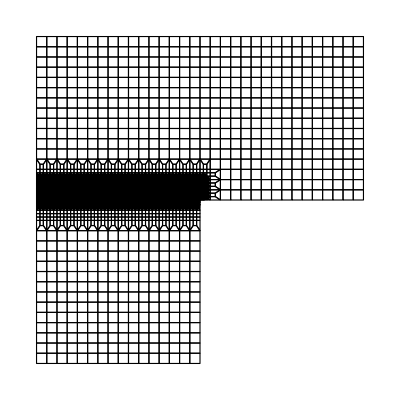

```mathematica
ShowMesh[m1]
```

```mathematica
ele//Dimensions
```

{29795,4}

```mathematica
loadLshape={{0.00000,0.00000},{0.02215,1.18261},{0.04696,2.52174},{0.06468,3.44348},{0.07975,4.17391},{0.09392,4.81739},{0.10810,5.42609},{0.12316,6.00000},{0.14089,6.60870},{0.15595,6.92174},{0.16835,7.13043},{0.17810,7.18261},{0.18962,7.16522},{0.19937,7.02609},{0.21177,6.80000},{0.22152,6.52174},{0.23127,6.22609},{0.24101,5.89565},{0.24987,5.58261},{0.25873,5.26957},{0.26671,4.97391},{0.27823,4.59130},{0.28797,4.29565},{0.29684,4.06957},{0.30658,3.79130},{0.31722,3.56522},{0.32962,3.26957},{0.34025,3.09565},{0.35089,2.85217},{0.36506,2.62609},{0.38278,2.34783},{0.39519,2.17391},{0.41203,1.96522},{0.43506,1.75652},{0.45544,1.60000},{0.47405,1.47826},{0.49532,1.30435},{0.51835,1.16522},{0.54759,1.07826},{0.57241,0.95652},{0.59278,0.86957},{0.61937,0.80000},{0.65127,0.71304},{0.67519,0.67826},{0.69025,0.66087},{0.69734,0.64348}};
```

```mathematica
fixBottom=FindPoints[coord,{0,0}-0.01,{0.25,0}+0.0001];
fixFun[xyz_List]:=ConstantArray[0,2];
fixValues1=BCValuesFunc[fixBottom,coord,fixFun,2];
dofFix1=DofIndexValue[fixBottom,fixValues1];
fixU=FindPoints[coord,{0.468,0.25}-0.001,{0.48,0.25}+0.001];
fixFun2[xyz_List]:={ 0,1 10^-3};
fixValues2=BCValuesFunc[fixU,coord,fixFun2,2];
dofFix2=DofIndexValue[fixU,fixValues2];
dofFix=Join[dofFix1,dofFix2,2];
```

```mathematica
coord[[783]]
```

{0.46875,0.25}

```mathematica
ndim=2;gpr=(*Q9ic3m;*)Q4ic2m;endn=ElementShapeNdN["Q1"(*"Q2S"*),gpr];endnN=endn[[All,1]];endndN=endn[[All,2;;]];
weighL=gpr[[All,-1]];

gprB=L2ic21m;
endnB=ElementShapeNdN["L1",gprB];endnNB=endnB[[All,1]];endndNB=endnB[[All,2;;]];
weighLB=gprB[[All,-1]];
```

```mathematica
{Rindex,Kindex}=RKindexFEM[ele,2];
```

```mathematica
dx
```

0.000578704

```mathematica
0.5 0.5/dx^2
```

746496.

```mathematica
lc0=0.7dx 2 2 2 2 2;morder0=1;mat0={25.85 10^9,0.18(* 0.18*),0,95 (*1000000*),lc0,0,morder0};
islinear=True;dt=0.2/4;dt=0.0005  (*20*);dt0=0.05/4;dtMin= 10^-4;nnode=Length[coord];ndof=nnode ndim;
uvw=ConstantArray[0.,{nnode,ndim}];pMid={1};fPMid={};ctime=0.;
(*ResiBC=ResidualOfElementSet[weighLB,endnNB,endndNB,coord,forceEle,{10.^4,0}];*)
printInterval=20;freeInterval=60000;nonlinearStep=If[islinear,1,10];incHistory={};
Hdirect=Table[0.,{Length[ele]},{Length[weighL]}];
HdirectN1=Hdirect;
HdirectN2=Hdirect;
nGP=Length[weighL];
tTotle=10000;
forceList={};
tforceList=0.;
normIncL={};
```

```mathematica
AbortOnMessage[]
```

```mathematica
(*try real phase field method. It seems that the damage model is for brittle fracture. *)
```

$Aborted

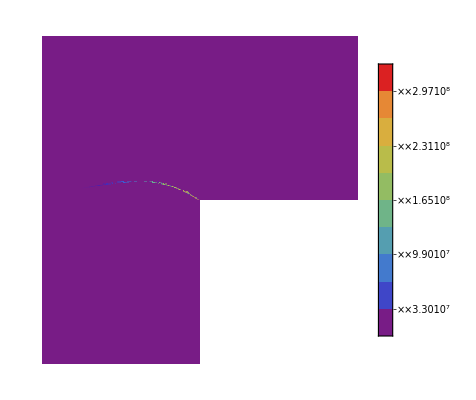

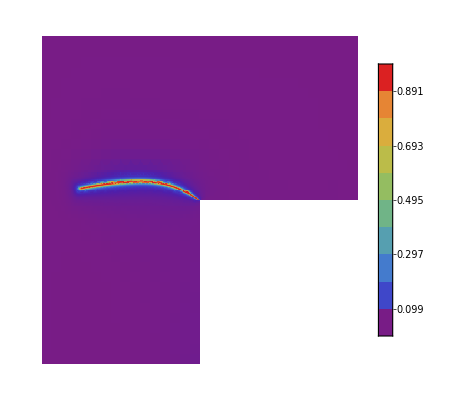

```mathematica
Do[
Label[dtHalf];
(*If[uvw[[faceList[[1]]]][[1]]>0.0005,dt=0.2 10^-3];*)
(*{clist,vlist}=AlphaMethod[duvw,uvw,dt];*)
(*nonvarList=NOMCombineVarsToArray[N[gm0],N[Df0],N[clist],N[vlist]];*)
(*HdirectMax=TwoTableMaxEach[HdirectMax,Hdirect[[All,All,1]]];
(*{Rp,Kp}=FemAllMatrixPFs[ls,weighL,endnN,endndN,coord,ele,HdirectMax];*)
{Rp,Kp}=FemAllMatrixPFsPara[ls,weighL,endnN,endndN,coord,ele,HdirectMax,RindexPf,KindexPf];
DirichletApply[Kp,Rp,pfdofFix,pDirichlet];
pfList=LinearSolve[Kp,Rp];*)
ctime+=dt;
uvwN=uvw;incT=ConstantArray[0.,ndof];
(*AppendTo[eH,{uvwN[[fixU[[1]]]][[2]],Max[Hdirect]/( mat0[[4]]/mat0[[5]])}];*)
normIncL={};
Do[
(*{Rsp,Ksp,Hdirect}=FemAllMatrixPFuvwPara[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,Rindex,Kindex,OneElementMatrixPFuvwPara2D];*)
{Rsp,Ksp,Hdirect}=FemAllMatrixVD2d[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrixVD2d];
(*Ksp100=Ksp[[1;;100,1;;100]];Abort[];*)
(*AppendTo[KList,Rsp];*)
(*FemAllMatrixPFuvw[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,MaximalEnergyDirection2D,WeakPlane2D];*)
(*Hdirect[[All,All,1]]*=ls;*)
Rsp*=-1.;
tforceList={10^3uvwN[[fixU[[1]]]][[2]],-0.1/10^3Total[ExtractNodeForce[Rsp,fixU,ndim,2]]};
(*Rsp+=ctime ResiBC;*)
NLDirichletApplySymF[ndim,uvwN,Ksp,Rsp,dofFix,ctime];
uv=LinearSolve[Ksp,Rsp,Method->"Pardiso"];
incT+=uv;
uvwN+=Vector2Matrix[uv,udim];
normInc=Norm[uv]/(Norm[incT]+10.^-20);
If[!NumericQ[normInc],Print["Error, symbol in nomrInc;"];Abort[]];
AppendTo[normIncL,normInc];
(*Print[normInc,"it",j];*)
If[Norm[uv]/(Norm[incT]+10.^-20)≤1. 10^-6,Break[]];kIti=j;If[(j==nonlinearStep || Total[normIncL]>5)&& (!islinear),Print["Warning, divergent at ctime=",ctime, " with dt=",dt];incHistory[[-1]]=100;
ctime-=dt;
dt=dt/2;
If[dt<dtMin,Print["Error, minimal time increment reached!"];Abort[]];
Goto[dtHalf]];,{j,nonlinearStep}];
If[ctime≥tTotle,Break[]];
Print["Step:",i," at time:",ctime," done!"];
uvw=uvwN;
dt=dt0 Max[ 1/(1+Max[Hdirect]/( mat0[[4]]/mat0[[5]]))^2, 40 10^-3];
AppendTo[forceList,tforceList];
AppendTo[incHistory,kIti];
If[kIti>15,dt=dt/2.];
If[Length[incHistory]>3 && Total[incHistory[[-3;;-1]]]<22 && !islinear,dt*=2.];
If[Mod[i-1,printInterval]==0,(*SaveToCell[uvw,"uvw"<>ToString[ctime]];*)Print[Plot2DField0[uvwN[[All,1]],m1]];Print[Plot2DField0[uvwN[[All,2]],m1]];(*Print[Plot2DField[pfList,m1]]*)];
AppendTo[fPMid,uvw[[pMid]]];
(*AppendTo[resP1,Flatten[uvw[[p1]]]];*)
(*Print[Plot2DField[ acc[[All,2]],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ acc[[All,1]],m1]];*)
(*Print[Contour2DField[NormList[ uvw],m1],Contour2DField[ NormList[acc],m1],Contour2DField[ NormList[vel],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ uvw[[All,2]],m1],Contour2DField[ acc[[All,1]],m1]];
Print[Contour2DField[ acc[[All,2]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ vel[[All,2]],m1]]*)
AbortCheck[],{i,2000}];
(*HnodeValue=GaussPointToNode[Hdirect,ele,coord,endnN];*)
HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
Plot2DField0[HnodeValue,m1]
Plot2DField0[HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),m1]
ListPlot[forceList,PlotRange->All]
SaveToCell[forceList,"Node lc:"<>ToString[Length[coord]]<>" and "<>ToString[N[lc0]]<>"fmax:"<>ToString[InputForm[Round1[forceList[[Ordering[forceList[[All,2]],-1]]],5]]]]
```